```mathematica
R=3
R2=2
```

3

2

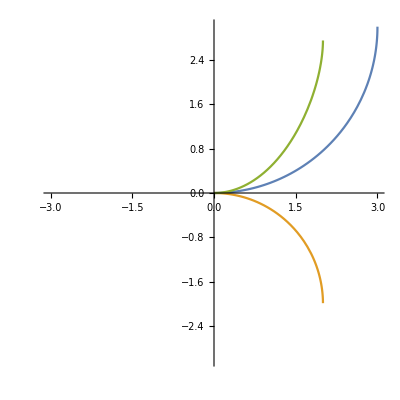

π/4

```mathematica
Plot[{R-R √(1 -(x/R)^2),-R2+ R2 √(1 -(x/R2)^2), R-R √(1 -(x/R)^2)+R2- R2 √(1 -(x/R2)^2)},{x,0,R}, PlotRange->{{-R,R},{-R,R}},AspectRatio->1]
```

```mathematica
y[x_]:=(R-R √(1 -(x/R)^2))
circ[x_]:=R √(1 -(x/R)^2)
```

π/5

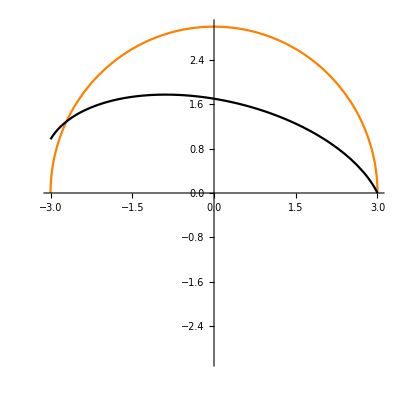

```mathematica
Theta = π/5
Plot[{ circ[x],  (√(c^2 Rad^2 ((c^2+2) s^2+s^4+1)-c^4 (2 s^2 xp+xp)^2)+c^3 s xp-c (s^3+s) xp)/((c^2+2) s^2+s^4+1)/.{xp-> x,Rad-> R,s-> Sin[Theta],c-> Cos[Theta]}  },{x,-R,R}, PlotRange->{{-R,R},{-R,R}},AspectRatio->1,PlotStyle->{Orange,Black}]
```

```mathematica
R1-R1 √(1 -(x/R1)^2)-(-R22+ R22 √(1 -(x/R22)^2))//FullSimplify
```

R1 (-√(1-x^2/R1^2))+R1-R22 √(1-x^2/R22^2)+R22

```mathematica
Solve[yp == -s c *xp +s^2 yp + c (Rad-Rad √(1 -(c xp - s yp)^2/Rad^2)),yp]/.c-> Cos[ß]/.s-> Sin[ß]//Simplify//PowerExpand//Simplify
```

{{yp→Rad cos(ß)-(√(Rad^2 cos(2 ß)+Rad^2+4 Rad xp sin(ß)-2 xp^2))/(√2)},{yp→(√(Rad^2 cos(2 ß)+Rad^2+4 Rad xp sin(ß)-2 xp^2))/(√2)+Rad cos(ß)}}

```mathematica
Rad Cos[ß]-(√(Rad^2 Cos[2 ß]+Rad^2+4 Rad xp Sin[ß]-2 xp^2))/(√2)//InputForm
```

Rad*Cos[ß] - Sqrt[Rad^2 - 2*xp^2 + Rad^2*Cos[2*ß] + 4*Rad*xp*Sin[ß]]/Sqrt[2]

π/6

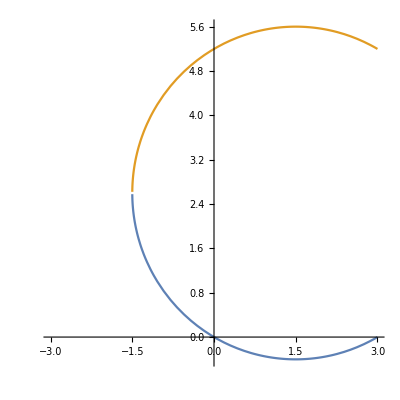

```mathematica
Theta=π/6
Plot[ {Rad*Cos[ß]-Sqrt[Rad^2-2*xp^2+Rad^2*Cos[2*ß]+4*Rad*xp*Sin[ß]]/Sqrt[2]/.Rad->R/.ß->Theta,(√(Rad^2 cos(2 ß)+Rad^2+4 Rad xp sin(ß)-2 xp^2))/(√2)+Rad cos(ß)/.Rad->R/.ß->Theta},{xp,-R,R},AspectRatio->1]
```

```mathematica
Tilted[ß_,Rad_,xp_]:=(√(Rad^2 Cos[2 ß]+Rad^2-4 Rad xp Sin[ß]-2 xp^2))/(√2)-Rad Cos[ß]
```

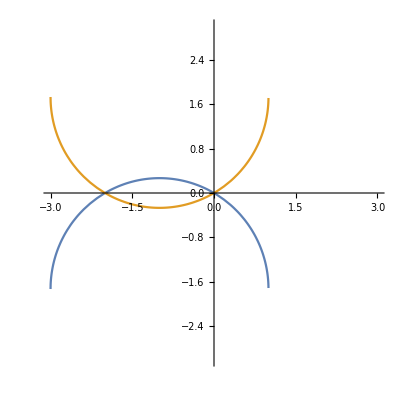

```mathematica
Plot[{Tilted[Theta,2,x],-Tilted[Theta,2,x]},{x,-R,R},PlotRange->{{-R,R},{-R,R}},AspectRatio->1]
```

```mathematica
Sep[ß_, Rad1_, Rad2_, xp_] := Abs[Evaluate[Tilted[ß, Rad1, xp] + Tilted[ß, Rad2, xp]]]
```

```mathematica
Sep[0,3,2,0.1]//N
```

0.00416869

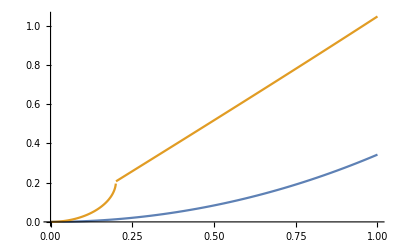

```mathematica
Plot[{Sep[0,3,3,x],Sep[0,3,0.2,x]},{x,0,1}]
```

```mathematica
Sep[ß, Rad1, Rad2, x]
```

Abs[(√(Rad1^2 cos(2 ß)+Rad1^2-4 Rad1 x sin(ß)-2 x^2))/(√2)-Rad1 cos(ß)+(√(Rad2^2 cos(2 ß)+Rad2^2-4 Rad2 x sin(ß)-2 x^2))/(√2)-Rad2 cos(ß)]

```mathematica
Sep[0.5, 2000,3000, 10]//N
```

10.9879

```mathematica
Solve[Sep[ß, Rad1, Rad2, x]==H&&ß>0&&Rad1>0&&Rad2>0&&H>0&&x>0,xp]
```

$Aborted